```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/dnaneet/Research_4.0/IEEE_Oceans/code/main/05152018a/wec

#### Buoy characteristics

```mathematica
{R=0.631(*buoy radius*),h=10(*buoy height*),ρ=1025(*sea water density*),g=9.81, λ=3., σ=0.06,m=550.,mSup=1000;Cd=0.75,τ=400,tMax=24.};
```

#### Trochoidal (Grestner) wave incident with Point Absorber type device based on the FlanSea WEC

```mathematica
r=λ σ;
(*interpolation function for trochoidal waveform*)
pts=Table[{ϕ-r Sin[2π ϕ/λ],ϕ},{ϕ,0,10π,π/100}];
if=Interpolation[pts];
wave[t_]=r Cos[2π if[t]/λ] +0.1RandomReal[{-1,1}];
y0=wave[0];
```

```mathematica
a33=1.; (*Arbitrary Value*)
A=.1;ω=1.;
b33=ρ g^2 A^2/(ω^3); 
eom={m y''[t]+a33 y''[t]==(*gravity*)-m g+(*buoyancy*)g π ρ R^2(wave[t]-y[t])-
(*downward only drag force*)UnitStep[y'[t]]0.5π R^2 Cd ρ  y'[t]^2-
(*reactive torque of the winch*) τ/.25(*winch radius*)-b33 y'[t],y[0]==y0,y'[0]==0.0001};
sol=NDSolveValue[eom,y,{t,0,tMax}];
solTable=Table[sol[tt],{tt,0,tMax,0.005}];
```

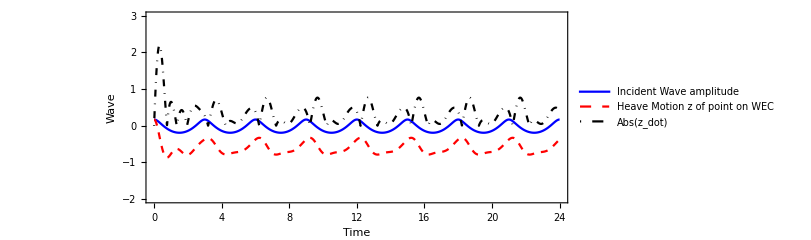

-Graphics-

```mathematica
Plot[{wave[t],sol[t],Abs[sol'[t]]},{t,0,tMax},Frame->True, FrameStyle->Black,PlotStyle->{{Thick,Blue},{Dashed,Red}, {DotDashed,Black}},BaseStyle->{FontSize->14},PlotRange->{All,{-2,3}},FrameLabel->{"Time","Wave"},AspectRatio->0.4,PlotLegends->Placed[{"Incident Wave amplitude","Heave Motion z of point on WEC", "Abs(z_dot)"},Above],ImageSize->600]
(*Export["./WECGrestner.pdf",%,ImageResolution->450]*)
ϵ=0.05;
rp1=MatrixPlot[
UnitStep[
ϵ-DistanceMatrix[solTable]
],FrameStyle->Black,BaseStyle->{FontSize->14},FrameLabel->{"Time (1000 divisions)","Time (1000 divisions)"}
]
(*Export["./WECGrestnerRP.pdf",%,ImageResolution->450]*)
```

#### Kuramoto - Sivashinsky wave incident with with Point Absorber type device

```mathematica
λ=1;a=1;x0=50.;ν=1.;tmax=250.;Subscript[δ, 0]=1;
Subscript[δ, 1]=0.15;(*RandomReal[{-1,1}]*)
Subscript[δ, 2]=1;(*2RandomReal[{-1,1}]*)
Subscript[δ, 3]=-1;(*5RandomReal[{-1,1}]*)
dvar[t_]:=  Piecewise[{{0,t≤50},{Subscript[δ, 1],500<t≤ 100}, {Subscript[δ, 2],1000<t≤150}, {Subscript[δ, 3],t>150}}];
ks=D[u[t, x], {t}] + u[t, x]*D[u[t, x], {x}] + D[u[t, x], {x, 2}] + dvar[t]*D[u[t, x], {x, 3}] + D[u[t, x], {x, 4}] ;
(*ks=D[u[t, x], {t}] + u[t, x]*D[u[t, x], {x}] + D[u[t, x], {x, 2}] + 0.15*D[u[t, x], {x, 3}] + D[u[t, x], {x, 4}] ;*)
sol=NDSolveValue[{ks==0,u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2) ,u[t,-x0]==u[t,x0]},u,{t,0,tmax},{x,-x0,x0}];
```

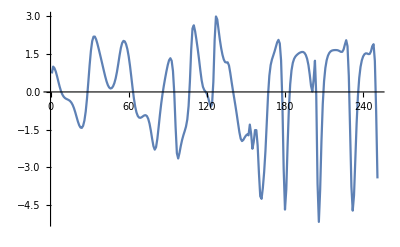

```mathematica
ksdata=Table[sol[t,0],{t,0,tmax,1}];
ListLinePlot[ksdata]
ifks=Interpolation[ksdata];
```

```mathematica
r=λ σ;
wave[t_]=r Cos[2π ifks[t]/λ]+0.1RandomReal[{-1,1}];
y0=wave[1]-m/ρ;
```

```mathematica
eom={m y''[t]==(*gravity*)-m g+(*buoyancy*)g π ρ R^2(wave[t]-y[t])-
(*downward only drag force*)UnitStep[y'[t]]0.5π R^2 Cd ρ  y'[t]^2-
(*reactive torque of the winch*) τ/.25(*winch radius*),y[1]==y0,y'[1]==0.0001};
sol=NDSolveValue[eom,y,{t,1,tMax}];
solTable=Table[sol[tt],{tt,1,tMax,0.01}];
```

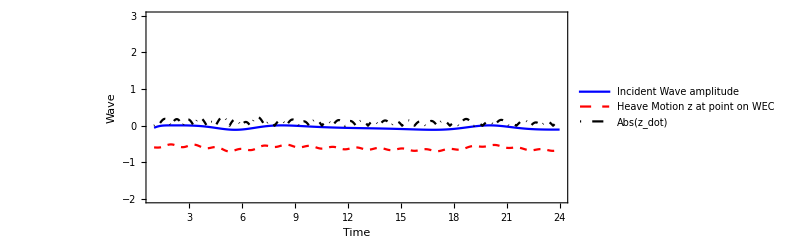

./WECKuramoto.pdf

-Graphics-

./WECKuramotoRP.pdf

```mathematica
Plot[{wave[t],sol[t],Norm[sol'[t],2]},{t,1,tMax},Frame->True, FrameStyle->Black,PlotStyle->{{Thick,Blue},{Dashed,Red}, {DotDashed,Black}},BaseStyle->{FontSize->14},PlotRange->{All,{-2,3}},FrameLabel->{"Time","Wave"},AspectRatio->0.4,PlotLegends->Placed[{"Incident Wave amplitude","Heave Motion z at point on WEC", "Abs(z_dot)"},Above],ImageSize->600]
Export["./WECKuramoto.pdf",%,ImageResolution->450]
ϵ=0.05;
rp2=MatrixPlot[
UnitStep[
ϵ-DistanceMatrix[solTable]
],FrameStyle->Black,BaseStyle->{FontSize->14},FrameLabel->{"Time (1000 divisions)","Time (1000 divisions)"}
]
Export["./WECKuramotoRP.pdf",%,ImageResolution->450]
```

#### Pierson - Moskowitz wave incident with with Point Absorber type device

```mathematica
data=Import["pm_waveElevation.mat", "MAT"];
```

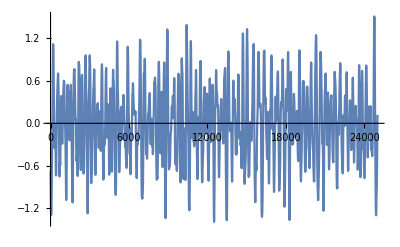

```mathematica
ListLinePlot[data//Flatten]
```

```mathematica
ifpm=Interpolation[Flatten[data][[1;;24000]]]
```

InterpolatingFunction[{{1., 24000.}}, <>]

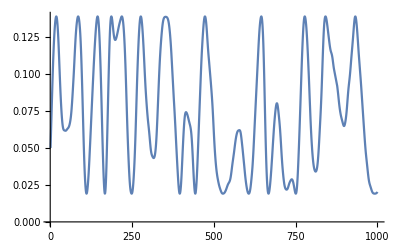

```mathematica
r=λ σ;
wave[t_]=r Cos[2π ifpm[t]/λ]+0.1RandomReal[{-1,1}];
Plot[wave[t],{t,1,1000}]
y0=wave[1]-m/ρ;
```

```mathematica
eom={m y''[t]==(*gravity*)-m g+(*buoyancy*)g π ρ R^2(wave[t]-y[t])-
(*downward only drag force*)UnitStep[y'[t]]0.5π R^2 Cd ρ  y'[t]^2-
(*reactive torque of the winch*) τ/.25(*winch radius*),y[1]==y0,y'[1]==0.0001};
sol=NDSolveValue[eom,y,{t,1,10*tMax}];
```

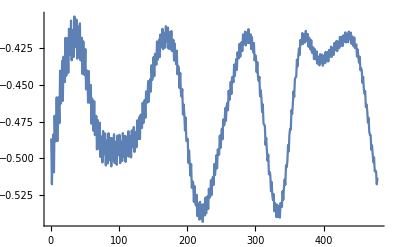

```mathematica
solTable=Table[sol[tt],{tt,1,10*tMax,0.5}];
ListLinePlot[solTable]
```

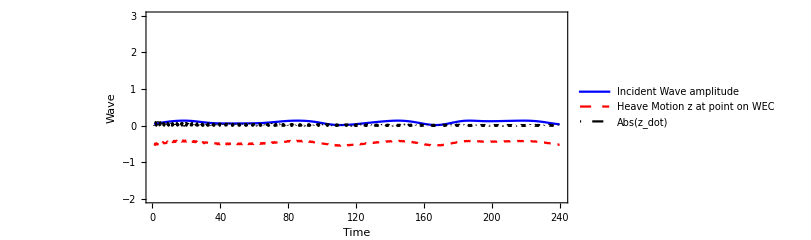

./WECPiersoMoskowitz.pdf

```mathematica
Plot[{wave[t],sol[t],Norm[sol'[t],2]},{t,1,10*tMax},Frame->True, FrameStyle->Black,PlotStyle->{{Thick,Blue},{Dashed,Red}, {DotDashed,Black}},BaseStyle->{FontSize->14},PlotRange->{All,{-2,3}},FrameLabel->{"Time","Wave"},AspectRatio->0.4,PlotLegends->Placed[{"Incident Wave amplitude","Heave Motion z at point on WEC", "Abs(z_dot)"},Above],ImageSize->600]
Export["./WECPiersoMoskowitz.pdf",%,ImageResolution->450]
```

```mathematica
ϵ=0.01;
rp2=MatrixPlot[
UnitStep[
ϵ-DistanceMatrix[solTable]
],FrameStyle->Black,BaseStyle->{FontSize->14},FrameLabel->{"Time (1000 divisions)","Time (1000 divisions)"}
]
Export["./WECPiersoMoskowitzRP.pdf",%,ImageResolution->450]
```

-Graphics-

./WECPiersoMoskowitzRP.pdf

#### Buoy 42040 with wec

```mathematica
data=Import["42040h2006.txt", "Data"];
```

```mathematica
data[[6;;2000]][[1;;10]][[9]]
```

{2006,1,1,12,0,999,6.2,7.4,0.6,5.,4.19,140,1013.3,22.7,22.7,999.,99.,99.}